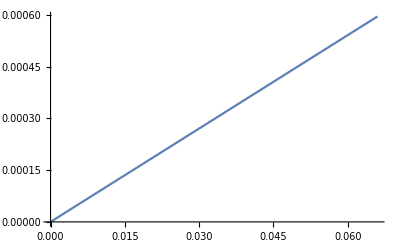

1.22217×10^-6

63.9641

```mathematica
T=(V*(m*g*L0*t1+2*Sqrt[m*g*IC*hc]))/(Pi*(r)^2*Lp*v*R*t1)+249.15;
Tmax=312.67;
dP= (T-249.15)*v*R/V;
P=(T*v*R)/V;
{m,g,ρ,hc,L0,Lp,v,R,r,V,t1,t2,IC}={0.006,9.8,1.17,0.000298,0.0125,0.0135,0.0175,8.3138,0.00875,0.00033,0.013,0.033,21.02*10^(-7)};a=dP/(t2^2);
b=-2a*t2;
c=(hc)/t2;
h[t]=c*t;
H[t]=hc-c*(t-t2);
Vspeed[t]=Sqrt[(2*(a*t^2+b*t+dP))/ρ];
Plot[Vspeed[t],{t,0,t2}];
Plot[a*t^2+b*t+dP,{t,0,t2}];
Plot[c*t,{t,0,2t2}]
Vloss1=Integrate[2.2*Pi*h[t]*((Vspeed[t]*t)^2+2*Vspeed[t]*L0*t),{t,0,t2}]
(*Vloss2=Integrate[Pi*(H[t])*((Vspeed[t]*t)^2+2*Vspeed[t]*L0*t),{t,0,t2}]*)
vloss=(Vloss1)*1000/22.4;
n=(v-(P*V)/(R*Tmax))/(vloss)
```